```mathematica
Exit[]
```

# QNMs of Halo Black Holes

```mathematica
(*Quit*)
```

```mathematica
(* non grid-based interpolation scheme to calculate QNMs of Schwarzschild black holes, I may have modified their method a bit. 
A HUGE CAUTION: any number you use has to be Rationalized or for large amount of grid points the code fail to work due to the differentiation matrices obtaining zero values*)
(* Main method taken from [arxiv:1610.08135v4] *)
```

```mathematica
SetDirectory[NotebookDirectory[]];
path=SetDirectory[NotebookDirectory[]];
```

```mathematica
<<HaloFlux`
```

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
n=17;
```

#### Differentiation matrices from built-in finite difference Mathematica functions

```mathematica
(*The above commented out code also calculates the differentiation matrices in the range we want but takes more time. It might be more accurate later when we deal with dirty black holes but for Schwarzschild the following method is enough.*)
min=0;
max=1;
 (*number of grid points used to discretize the metric components of spacetime, the compactified radial coordinate [0,1] and build the differentiation matrices*)
di=(max-min)/(n-1);(*equispaced data points*)
x=Table[i,{i,min,max,di}];
DF0=NDSolve`FiniteDifferenceDerivative[Derivative[0],Range[0,1,1/(n-1)],DifferenceOrder->n]["DifferentiationMatrix"] ;(*zeroth derivative*)
DF1=NDSolve`FiniteDifferenceDerivative[Derivative[1],Range[0,1,1/(n-1)],DifferenceOrder->n-1]["DifferentiationMatrix"]; (*first derivative*)
DF2=NDSolve`FiniteDifferenceDerivative[Derivative[2],Range[0,1,1/(n-1)],DifferenceOrder->n-2]["DifferentiationMatrix"]; (*second derivative*)
```

```mathematica
(* I delete the first and last entry in order to avoid calculating the functions at the extrema of the domain: 0 (rh) and 1 (∞), which are singular points *)
Delete[DF0,{{1},{n}}];
df0=Delete[Transpose[%],{{1},{n}}]//Transpose;
Delete[DF1,{{1},{n}}];
df1=Delete[Transpose[%],{{1},{n}}]//Transpose;
Delete[DF2,{{1},{n}}];
df2=Delete[Transpose[%],{{1},{n}}]//Transpose;
```

## Fixing a0

## Finding modes

```mathematica
δω[z_,l_,a0_,ωtrial_]:=Block[{mbh=1,M,ρmetric,f,m,fh,derfh,derrmh,rh,r,t0,ω,l0,s0,Mt0,Ml0,Ms0,FM0,eq,sol},

rh=2mbh(1+10^-4);
M=a0 z;

ρmetric=background["HQ",M,a0,10^10][[1,{1,3}]];

f[r_]=ρmetric[[1,2]][r];
m[r_]=ρmetric[[2,2]][r];

fh=0;
derfh=f'[rh];
derrmh=(D[ρprofile[r,M,a0,"HQ"],r]//.r->rh)*16 π;

t0=Table[f[-rh/(-1+x⟦i⟧)] (2 m[-rh/(-1+x⟦i⟧)]+rh/(-1+x⟦i⟧)) (1-x⟦i⟧)^3 (-1+x⟦i⟧)^2 x⟦i⟧,{i,2,n-1}]//FullSimplify;

l0=Table[1/(√(rh derfh))f[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧)^2 (2 m[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧) ((-1+x⟦i⟧) (-2+(1+4 ⅈ M ω) x⟦i⟧) √(rh derfh)+2 ⅈ rh ω (1-2 x⟦i⟧ (1+√(rh derfh))+x⟦i⟧^2 (1+√(rh derfh))))+rh (2 (-1+x⟦i⟧) (-1+(1+2 ⅈ M ω) x⟦i⟧) √(rh derfh)+2 ⅈ rh ω (1-2 x⟦i⟧ (1+√(rh derfh))+x⟦i⟧^2 (1+√(rh derfh)))-(-1+x⟦i⟧) x⟦i⟧ √(rh derfh)(m'[-rh/(-1+x⟦i⟧)]))),{i,2,n-1}]//FullSimplify;

s0=Table[1/(x⟦i⟧ derfh)f[-rh/(-1+x⟦i⟧)] (rh+2 m[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧)) ((-2+2 (5+2 ⅈ M ω+2 ⅈ rh ω) x⟦i⟧+(-20-17 ⅈ rh ω+4 M^2 ω^2+4 rh^2 ω^2+2 M ω (-9 ⅈ+4 rh ω)) x⟦i⟧^2-2 (-9-9 ⅈ rh ω+4 M^2 ω^2+2 rh^2 ω^2+6 M ω (-2 ⅈ+rh ω)) x⟦i⟧^3+(-6-5 ⅈ rh ω+4 M^2 ω^2+rh^2 ω^2+2 M ω (-5 ⅈ+2 rh ω)) x⟦i⟧^4) derfh+ω (-1+x⟦i⟧)^2 ((-1+x⟦i⟧) (3 ⅈ+(-5 ⅈ+4 M ω) x⟦i⟧) √(rh derfh)+rh ω (1-2 x⟦i⟧ (1+2 √(rh derfh))+x⟦i⟧^2 (1+2 √(rh derfh)))))+1/(√(rh derfh))f[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧) ((-1+x⟦i⟧) (-1+(2+2 ⅈ M ω) x⟦i⟧) √(rh derfh)+ⅈ rh ω (1-2 x⟦i⟧ (1+√(rh derfh))+x⟦i⟧^2 (1+√(rh derfh)))) (6 m[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧)+rh (2+m'[-rh/(-1+x⟦i⟧)]))+(1-x⟦i⟧)^3 x⟦i⟧ ((rh^3 ω^2)/(-1+x⟦i⟧)^3+f[-rh/(-1+x⟦i⟧)] (-6 m[-rh/(-1+x⟦i⟧)]-(rh (l+l^2+m'[-rh/(-1+x⟦i⟧)]))/(-1+x⟦i⟧))),{i,2,n-1}]//FullSimplify;

Mt0=t0*IdentityMatrix[n-2];
Ml0=l0*IdentityMatrix[n-2];
Ms0=s0*IdentityMatrix[n-2];

(*ωtrial=SetPrecision[0.37367-0.08897056I,50];*)
FM0=Mt0.df2+Ml0.df1+Ms0.df0;
eq=Det[N[FM0,80]];
(*Precision[FM0]*)
(*Print[Precision[eq]];*)
sol=FindRoot[eq==0,{ω,ωtrial},WorkingPrecision->Precision[eq]];
PrintTemporary[{Re[sol[[1,2]]],Im[sol[[1,2]]]}];
Return[{z,Re[sol[[1,2]]],Im[sol[[1,2]]]}]
]
```

```mathematica
(*compactness=Range[-6,-1,1/2]*)
```

```mathematica
compactness={-6,-3,-25/12,-25/13, -7/4,-3/2,-13/10};
```

#### fundamental

```mathematica
l2n0=Monitor[Table[δω[10^compactness[[ii]],2,20,SetPrecision[0.37-0.08I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
l3n0=Monitor[Table[δω[10^compactness[[ii]],3,20,SetPrecision[0.59-0.09I,50]],{ii,1,Length[compactness]}],ii];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50.6567 digits of working precision to meet these tolerances.

```mathematica
l4n0=Monitor[Table[δω[10^compactness[[ii]],4,20,SetPrecision[0.81-0.09I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
ReIm20a0l2n0=l2n0[[;;,2;;3]];
ReIm20a0l3n0=l3n0[[;;,2;;3]];
ReIm20a0l4n0=l4n0[[;;,2;;3]];
```

#### first overtone

```mathematica
l2n1=Monitor[Table[δω[10^compactness[[ii]],2,20,SetPrecision[0.35-0.27I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
l3n1=Monitor[Table[δω[10^compactness[[ii]],3,20,SetPrecision[0.58-0.28I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
l4n1=Monitor[Table[δω[10^compactness[[ii]],4,20,SetPrecision[0.79-0.28I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
ReIm20a0l2n1=l2n1[[;;,2;;3]];
ReIm20a0l3n1=l3n1[[;;,2;;3]];
ReIm20a0l4n1=l4n1[[;;,2;;3]];
```

#### second overtone

```mathematica
l2n2Vac=δω[0,2,20,SetPrecision[0.30-0.47I,50]];
```

```mathematica
l3n2Vac=δω[0,3,20,SetPrecision[0.56-0.48I,50]];
```

```mathematica
l4n2Vac=δω[0,4,20,SetPrecision[0.80-0.48I,50]];
```

Divide::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

FindRoot::jsing: Encountered a singular Jacobian at the point {ω} = {0.0101845623845005930403196605444621202866860846-0.60083467358932378524229234942455681254658287 ⅈ}. Try perturbing the initial point(s).

```mathematica
l2n2=Monitor[Table[δω[10^compactness[[ii]],2,20,SetPrecision[0.3-0.47I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
l3n2=Monitor[Table[δω[10^compactness[[ii]],3,20,SetPrecision[0.56-0.48I,50]],{ii,1,Length[compactness]}],ii];
```

Divide::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

FindRoot::jsing: Encountered a singular Jacobian at the point {ω} = {0.0216572143607768059780926961366276373155415058-0.257377221649129205244613260994412939908215776 ⅈ}. Try perturbing the initial point(s).

```mathematica
l4n2=Monitor[Table[δω[10^compactness[[ii]],4,20,SetPrecision[0.80-0.48I,50]],{ii,1,Length[compactness]}],ii];
```

Divide::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

FindRoot::jsing: Encountered a singular Jacobian at the point {ω} = {-0.388855774519478713018847796544203763559785965-1.84733674098201621648256784955406856566814192 ⅈ}. Try perturbing the initial point(s).

Divide::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

FindRoot::jsing: Encountered a singular Jacobian at the point {ω} = {0.768284187097340930621866124059308373623579605-1.05705607085972940421600211025494160697086276 ⅈ}. Try perturbing the initial point(s).

Divide::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Divide::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {ω} = {0.555074702427843266838668575672440698570185758-0.797107614951289131655074864055207530102196898 ⅈ}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

```mathematica
l2n2T=Join[{l2n2Vac},l2n2];
l3n2T=Join[{l3n2Vac},l3n2];
l4n2T=Join[{l4n2Vac},l4n2];
```

```mathematica
datasetR[data_,thresh_]:=Select[Thread[{data[[2;;-1,1]],Abs[data[[2;;-1,2]]/data[[1,2]]-1]}],#[[1]]<=thresh&];
datasetI[data_,thresh_]:=Select[Thread[{data[[2;;-1,1]],Abs[data[[2;;-1,3]]/data[[1,3]]-1]}],#[[1]]<=thresh&];
```

```mathematica
line2n2R=Fit[datasetR[l2n2T,10^-2][[2;;-1]],{1,t,t^2},t]
line3n2R=Fit[datasetR[l3n2T,10^-2][[2;;-1]],{1,t,t^2},t]
line4n2R=Fit[datasetR[l4n2T,10^-2][[2;;-1]],{1,t,t^2},t]
```

0

0

74.924956382334148830006188153591583926926655-305.07940346592166752601991553837236957008366 t-183725.86190354184073807938098539779833325628 t^2

```mathematica
line2n2I=Fit[datasetI[l2n2T,10^-2][[2;;-1]],{1,t,t^2},t]
line3n2I=Fit[datasetI[l3n2T,10^-2][[2;;-1]],{1,t,t^2},t]
line4n2I=Fit[datasetI[l4n2T,10^-2][[2;;-1]],{1,t,t^2},t]
```

0

0

0.7763633858986924522758632533484821999040067-13.94858336684332746354053305015024199673073 t-3102.104173436334952255854143154340851559642 t^2

```mathematica
ReIm20a0l2n2=l2n2[[;;,2;;3]];
ReIm20a0l3n2=l3n2[[;;,2;;3]];
ReIm20a0l4n2=l4n2[[;;,2;;3]];
```

#### Export

```mathematica
Export["Matrix_Hern.m",{l2n0T,l3n0T, l4n0T,l2n1T,l3n1T, l4n1T}]
```

Matrix_Hern.m

## Finding modes (higher a0 fixed)

#### fundamental

```mathematica
l2n02=Monitor[Table[δω[10^compactness[[ii]],2,50,SetPrecision[0.37-0.08I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
l3n02=Monitor[Table[δω[10^compactness[[ii]],3,50,SetPrecision[0.59-0.09I,50]],{ii,1,Length[compactness]}],ii];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50.2023 digits of working precision to meet these tolerances.

```mathematica
l4n02=Monitor[Table[δω[10^compactness[[ii]],4,50,SetPrecision[0.81-0.09I,50]],{ii,1,Length[compactness]}],ii];
```

Power::infy: Infinite expression 1/(0.+0. ⅈ)^5 encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {ω} = {0.62720592122957286382456825642630720060840129054724-1.8994051614256356610822650590960358327202626401009 ⅈ}.

Power::infy: Infinite expression 1/(0.+0. ⅈ)^5 encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {ω} = {-0.178443941514648735380095138152873029496401009195652-1.61687583065881233144711950907443607759962796413886 ⅈ}.

```mathematica
ReIm104a0l2n0=l2n02[[;;,2;;3]];
ReIm104a0l3n0=l3n02[[;;,2;;3]];
ReIm104a0l4n0=l4n02[[;;,2;;3]];
```

#### first overtone

```mathematica
l2n12=Monitor[Table[δω[10^compactness[[ii]],2,50,SetPrecision[0.35-0.27I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
l3n12=Monitor[Table[δω[10^compactness[[ii]],3,50,SetPrecision[0.58-0.28I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
l4n12=Monitor[Table[δω[10^compactness[[ii]],4,50,SetPrecision[0.79-0.28I,50]],{ii,1,Length[compactness]}],ii];
```

Divide::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

FindRoot::jsing: Encountered a singular Jacobian at the point {ω} = {-0.129076365356005238877718564071966918833148909890228-0.280000000000000026645352591003756970167160034179688 ⅈ}. Try perturbing the initial point(s).

```mathematica
ReIm104a0l2n1=l2n12[[;;,2;;3]];
ReIm104a0l3n1=l3n12[[;;,2;;3]];
ReIm104a0l4n1=l4n12[[;;,2;;3]];
```

#### second overtone

```mathematica
l2n2Vac2=δω[0,2,100,SetPrecision[0.30-0.47I,50]];
```

```mathematica
l3n2Vac2=δω[0,3,100,SetPrecision[0.56-0.48I,50]];
```

```mathematica
l4n2Vac2=δω[0,4,100,SetPrecision[0.80-0.48I,50]];
```

```mathematica
l2n22=Monitor[Table[δω[10^compactness[[ii]],2,100,SetPrecision[0.3-0.47I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
l3n22=Monitor[Table[δω[10^compactness[[ii]],3,100,SetPrecision[0.56-0.48I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
l4n22=Monitor[Table[δω[10^compactness[[ii]],4,100,SetPrecision[0.80-0.48I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
l2n2T2=Join[{l2n2Vac2},l2n22];
l3n2T2=Join[{l3n2Vac2},l3n22];
l4n2T2=Join[{l4n2Vac2},l4n22];
```

```mathematica
datasetR[data_,thresh_]:=Select[Thread[{data[[2;;-1,1]],Abs[data[[2;;-1,2]]/data[[1,2]]-1]}],#[[1]]<=thresh&];
datasetI[data_,thresh_]:=Select[Thread[{data[[2;;-1,1]],Abs[data[[2;;-1,3]]/data[[1,3]]-1]}],#[[1]]<=thresh&];
```

```mathematica
ReIm104a0l2n2=l2n22[[;;,2;;3]];
ReIm104a0l3n2=l3n22[[;;,2;;3]];
ReIm104a0l4n2=l4n22[[;;,2;;3]];
```

## Finding modes (smaller a0 fixed)

#### fundamental

```mathematica
l2n02=Monitor[Table[δω[10^compactness[[ii]],2,2,SetPrecision[0.37-0.08I,50]],{ii,1,Length[compactness]}],ii];
```

Divide::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

FindRoot::jsing: Encountered a singular Jacobian at the point {ω} = {0.9867784092555139794595921934133780264365295929641-0.4956397359195165821672597360457407381453918382623 ⅈ}. Try perturbing the initial point(s).

```mathematica
l3n02=Monitor[Table[δω[10^compactness[[ii]],3,2,SetPrecision[0.59-0.09I,50]],{ii,1,Length[compactness]}],ii];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50.3156 digits of working precision to meet these tolerances.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50.0665 digits of working precision to meet these tolerances.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50.2555 digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

Power::infy: Infinite expression 1/(0.+0. ⅈ)^5 encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {ω} = {0.58999999999999996891375531049561686813831329345703-1.6868249324550709139409482698021342775116840572623 ⅈ}.

```mathematica
l4n02=Monitor[Table[δω[10^compactness[[ii]],4,2,SetPrecision[0.81-0.09I,50]],{ii,1,Length[compactness]}],ii];
```

Divide::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

FindRoot::jsing: Encountered a singular Jacobian at the point {ω} = {1.7968725375520081984691355995938889344880774386273-1.6132373155521090525537958441625859071763349567415 ⅈ}. Try perturbing the initial point(s).

Divide::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

FindRoot::jsing: Encountered a singular Jacobian at the point {ω} = {0.8100000000000000532907051820075139403343200683594-1.904984662432367545657927882159136164872253374392 ⅈ}. Try perturbing the initial point(s).

Divide::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Divide::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {ω} = {0.8100000000000000532907051820075139403343200683594-1.904984662432367545657927882159136164872253374392 ⅈ}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

Power::infy: Infinite expression 1/(0.+0. ⅈ)^5 encountered.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {ω} = {-0.40037194509463961902943773003685632922224203399022-1.4424677738831908083438672619941745727864339224954 ⅈ}.

```mathematica
ReIm104a0l2n0=l2n02[[;;,2;;3]];
ReIm104a0l3n0=l3n02[[;;,2;;3]];
ReIm104a0l4n0=l4n02[[;;,2;;3]];
```

#### first overtone

```mathematica
l2n12=Monitor[Table[δω[10^compactness[[ii]],2,2,SetPrecision[0.35-0.27I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
l3n12=Monitor[Table[δω[10^compactness[[ii]],3,2,SetPrecision[0.58-0.28I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
l4n12=Monitor[Table[δω[10^compactness[[ii]],4,2,SetPrecision[0.79-0.28I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
ReIm104a0l2n1=l2n12[[;;,2;;3]];
ReIm104a0l3n1=l3n12[[;;,2;;3]];
ReIm104a0l4n1=l4n12[[;;,2;;3]];
```

#### second overtone

```mathematica
l2n2Vac2=δω[0,2,2,SetPrecision[0.30-0.47I,50]];
```

```mathematica
l3n2Vac2=δω[0,3,2,SetPrecision[0.56-0.48I,50]];
```

```mathematica
l4n2Vac2=δω[0,4,2,SetPrecision[0.80-0.48I,50]];
```

```mathematica
l2n22=Monitor[Table[δω[10^compactness[[ii]],2,2,SetPrecision[0.3-0.47I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
l3n22=Monitor[Table[δω[10^compactness[[ii]],3,2,SetPrecision[0.56-0.48I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
l4n22=Monitor[Table[δω[10^compactness[[ii]],4,2,SetPrecision[0.80-0.48I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
l2n2T2=Join[{l2n2Vac2},l2n22];
l3n2T2=Join[{l3n2Vac2},l3n22];
l4n2T2=Join[{l4n2Vac2},l4n22];
```

```mathematica
datasetR[data_,thresh_]:=Select[Thread[{data[[2;;-1,1]],Abs[data[[2;;-1,2]]/data[[1,2]]-1]}],#[[1]]<=thresh&];
datasetI[data_,thresh_]:=Select[Thread[{data[[2;;-1,1]],Abs[data[[2;;-1,3]]/data[[1,3]]-1]}],#[[1]]<=thresh&];
```

```mathematica
ReIm104a0l2n2=l2n22[[;;,2;;3]];
ReIm104a0l3n2=l3n22[[;;,2;;3]];
ReIm104a0l4n2=l4n22[[;;,2;;3]];
```

## plots (fixed a0)

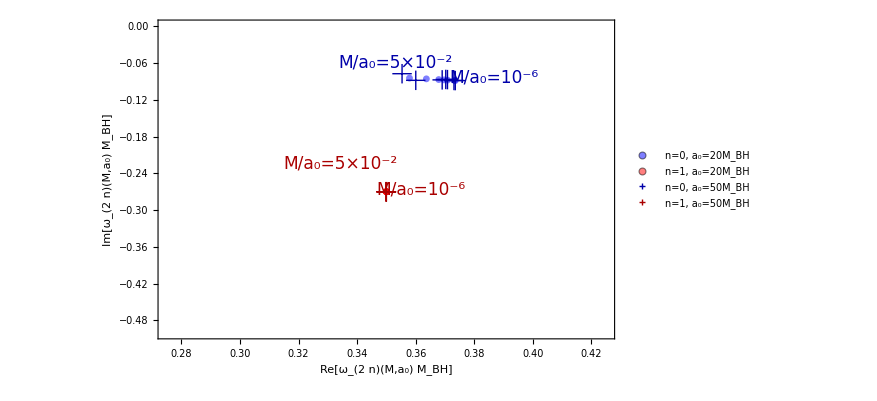

./plot/N=17 ReIm/3_l2_cp_n17.pdf

```mathematica
l2=ListPlot[{ReIm20a0l2n0,ReIm20a0l2n1,ReIm104a0l2n0,ReIm104a0l2n1},Frame->True,ImageSize->650,PlotRange->{{0.275,0.425},{-0.5,0.0}},FrameStyle->Directive[Thickness[0.0025],Black],FrameTicks->True,FrameLabel->{Style["Re[ω_(2  n)(M,a_0) M_BH]",Black,20],Style["Im[ω_(2  n)(M,a_0) M_BH]",Black,20]},FrameTicksStyle->Directive[Black,20],LabelStyle->{FontSize->19,FontFamily->"Times"},PlotMarkers->{Graphics[{Blue,Opacity[0.5],Thick,Disk[]},ImageSize->7],Graphics[{Red,Opacity[0.5],Thick,Disk[]},ImageSize->7],Style["+",{Darker@Blue,FontSize->20}],Style["+",{Darker@Red,FontSize->20}],Style["+",{Darker@Green,FontSize->20}]},PlotLegends->Placed[LineLegend[{Style["n=0, a_0=20M_BH",FontSize->16],Style["n=1, a_0=20M_BH",FontSize->16],Style["n=0, a_0=50M_BH",FontSize->16],Style["n=1, a_0=50M_BH",FontSize->16]},"Spacings"->{0.3}],{0.15,0.75}],Epilog->{Text[Style["M/a_0=5×10^-2",17,FontFamily->"Times",Darker@Blue],Scaled[{0.52,0.867}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Blue],Scaled[{0.735,0.82}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Red],Scaled[{0.575,0.47}]],Text[Style["M/a_0=5×10^-2",17,FontFamily->"Times",Darker@Red],Scaled[{0.4,0.55}]](*,Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Green],Scaled[{0.45,0.07}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Green],Scaled[{0.1,0.16}]]*)}]
Export["./plot/N=17 ReIm/3_l2_cp_n17.pdf",%]
```

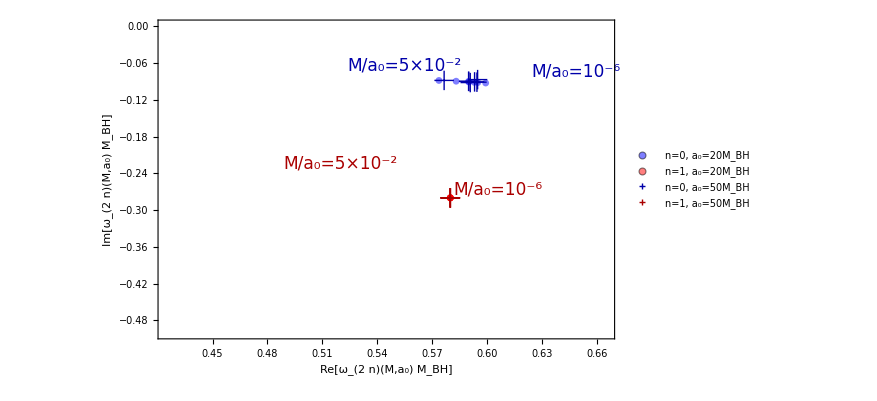

./plot/N=17 ReIm/3_l3_cp_n17.pdf

```mathematica
l3=ListPlot[{ReIm20a0l3n0,ReIm20a0l3n1,ReIm104a0l3n0,ReIm104a0l3n1},Frame->True,ImageSize->650,PlotRange->{{0.425,0.665},{-0.5,0.0}},FrameStyle->Directive[Thickness[0.0025],Black],FrameTicks->True,FrameLabel->{Style["Re[ω_(2  n)(M,a_0) M_BH]",Black,20],Style["Im[ω_(2  n)(M,a_0) M_BH]",Black,20]},FrameTicksStyle->Directive[Black,20],LabelStyle->{FontSize->19,FontFamily->"Times"},PlotMarkers->{Graphics[{Blue,Opacity[0.5],Thick,Disk[]},ImageSize->7],Graphics[{Red,Opacity[0.5],Thick,Disk[]},ImageSize->7],Style["+",{Darker@Blue,FontSize->20}],Style["+",{Darker@Red,FontSize->20}],Style["+",{Darker@Green,FontSize->20}]},PlotLegends->Placed[LineLegend[{Style["n=0, a_0=20M_BH",FontSize->16],Style["n=1, a_0=20M_BH",FontSize->16],Style["n=0, a_0=50M_BH",FontSize->16],Style["n=1, a_0=50M_BH",FontSize->16],Style["n=2, a_0=50M_BH",FontSize->16]},"Spacings"->{0.3}],{0.15,0.75}],Epilog->{Text[Style["M/a_0=5×10^-2",17,FontFamily->"Times",Darker@Blue],Scaled[{0.54,0.857}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Blue],Scaled[{0.915,0.84}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Red],Scaled[{0.745,0.47}]],Text[Style["M/a_0=5×10^-2",17,FontFamily->"Times",Darker@Red],Scaled[{0.4,0.55}]](*,Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Green],Scaled[{0.45,0.07}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Green],Scaled[{0.1,0.16}]]*)}]
Export["./plot/N=17 ReIm/3_l3_cp_n17.pdf",%]
```

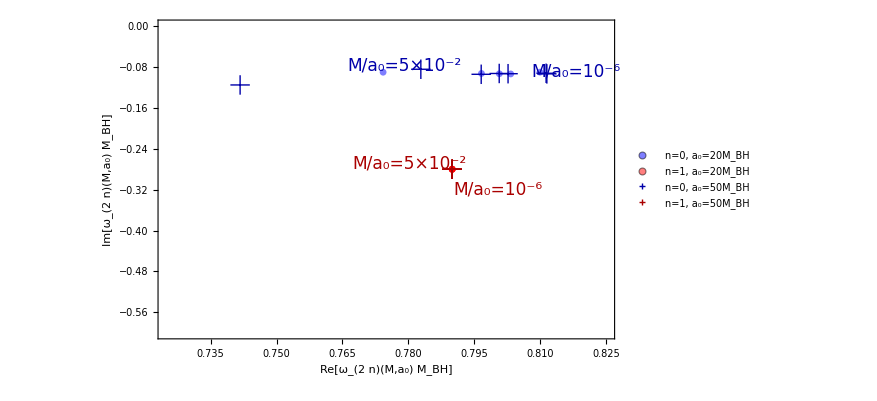

./plot/N=17 ReIm/3_l4_cp_n17.pdf

```mathematica
l4=ListPlot[{ReIm20a0l4n0,ReIm20a0l4n1,ReIm104a0l4n0,ReIm104a0l4n1},Frame->True,ImageSize->650,PlotRange->{{0.725,0.825},{-0.6,0.0}},FrameStyle->Directive[Thickness[0.0025],Black],FrameTicks->True,FrameLabel->{Style["Re[ω_(2  n)(M,a_0) M_BH]",Black,20],Style["Im[ω_(2  n)(M,a_0) M_BH]",Black,20]},FrameTicksStyle->Directive[Black,20],LabelStyle->{FontSize->19,FontFamily->"Times"},PlotMarkers->{Graphics[{Blue,Opacity[0.5],Thick,Disk[]},ImageSize->7],Graphics[{Red,Opacity[0.5],Thick,Disk[]},ImageSize->7],Style["+",{Darker@Blue,FontSize->20}],Style["+",{Darker@Red,FontSize->20}],Style["+",{Darker@Green,FontSize->20}]},PlotLegends->Placed[LineLegend[{Style["n=0, a_0=20M_BH",FontSize->16],Style["n=1, a_0=20M_BH",FontSize->16],Style["n=0, a_0=50M_BH",FontSize->16],Style["n=1, a_0=50M_BH",FontSize->16],Style["n=2, a_0=10^2M_BH",FontSize->16]},"Spacings"->{0.3}],{0.15,0.75}],Epilog->{Text[Style["M/a_0=5×10^-2",17,FontFamily->"Times",Darker@Blue],Scaled[{0.54,0.857}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Blue],Scaled[{0.915,0.84}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Red],Scaled[{0.745,0.47}]],Text[Style["M/a_0=5×10^-2",17,FontFamily->"Times",Darker@Red],Scaled[{0.55,0.55}]](*,Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Green],Scaled[{0.45,0.07}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Green],Scaled[{0.1,0.16}]]*)}]
Export["./plot/N=17 ReIm/3_l4_cp_n17.pdf",%]
```

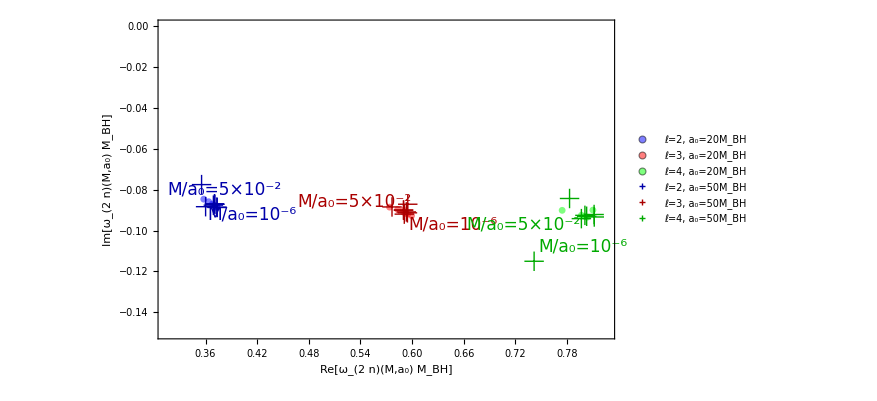

./plot/N=17 ReIm/3_all_l_cp_n17.pdf

```mathematica
lTot=ListPlot[{ReIm20a0l2n0,ReIm20a0l3n0,ReIm20a0l4n0,ReIm104a0l2n0,ReIm104a0l3n0,ReIm104a0l4n0},Frame->True,ImageSize->650,PlotRange->{{0.315,0.825},{-0.15,0.0}},FrameStyle->Directive[Thickness[0.0025],Black],FrameTicks->True,FrameLabel->{Style["Re[ω_ℓ0(M,a_0) M_BH]",Black,20],Style["Im[ω_ℓ0(M,a_0) M_BH]",Black,20]},FrameTicksStyle->Directive[Black,20],LabelStyle->{FontSize->19,FontFamily->"Times"},PlotMarkers->{Graphics[{Blue,Opacity[0.5],Thick,Disk[]},ImageSize->7],Graphics[{Red,Opacity[0.5],Thick,Disk[]},ImageSize->7],Graphics[{Green,Opacity[0.5],Thick,Disk[]},ImageSize->7],Style["+",{Darker@Blue,FontSize->20}],Style["+",{Darker@Red,FontSize->20}],Style["+",{Darker@Green,FontSize->20}]},PlotLegends->Placed[LineLegend[{Style["ℓ=2, a_0=20M_BH",FontSize->16],Style["ℓ=3, a_0=20M_BH",FontSize->16],Style["ℓ=4, a_0=20M_BH",FontSize->16],Style["ℓ=2, a_0=50M_BH",FontSize->16],Style["ℓ=3, a_0=50M_BH",FontSize->16],Style["ℓ=4, a_0=50M_BH",FontSize->16]},"Spacings"->{0.3}],{0.85,0.75}],Epilog->{Text[Style["M/a_0=5×10^-2",17,FontFamily->"Times",Darker@Blue],Scaled[{0.145,0.47}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Blue],Scaled[{0.205,0.39}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Red],Scaled[{0.645,0.36}]],Text[Style["M/a_0=5×10^-2",17,FontFamily->"Times",Darker@Red],Scaled[{0.43,0.43}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Green],Scaled[{0.93,0.29}]],Text[Style["M/a_0=5×10^-2",17,FontFamily->"Times",Darker@Green],Scaled[{0.8,0.36}]]}]
Export["./plot/N=17 ReIm/3_all_l_cp_n17.pdf",%]
```

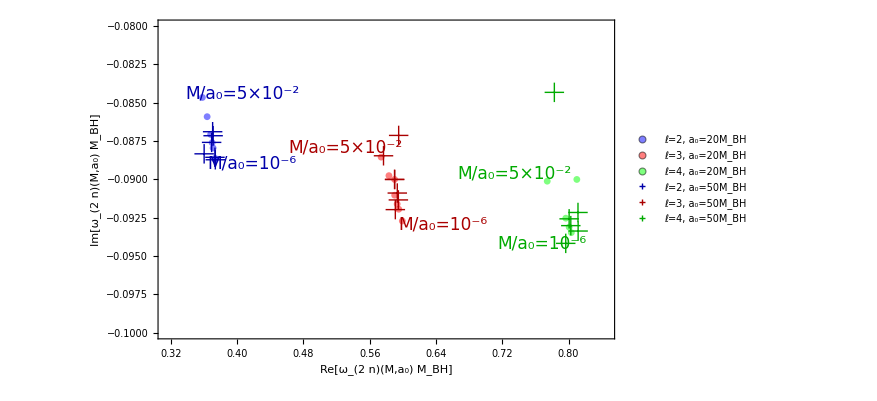

./plot/N=17 ReIm/3_all_l_cp_n17_2.pdf

```mathematica
lTot=ListPlot[{ReIm20a0l2n0,ReIm20a0l3n0,ReIm20a0l4n0,ReIm104a0l2n0,ReIm104a0l3n0,ReIm104a0l4n0},Frame->True,ImageSize->650,PlotRange->{{0.315,0.845},{-0.10,-0.08}},FrameStyle->Directive[Thickness[0.0025],Black],FrameTicks->True,FrameLabel->{Style["Re[ω_ℓ0(M,a_0) M_BH]",Black,20],Style["Im[ω_ℓ0(M,a_0) M_BH]",Black,20]},FrameTicksStyle->Directive[Black,20],LabelStyle->{FontSize->19,FontFamily->"Times"},PlotMarkers->{Graphics[{Blue,Opacity[0.5],Thick,Disk[]},ImageSize->7],Graphics[{Red,Opacity[0.5],Thick,Disk[]},ImageSize->7],Graphics[{Green,Opacity[0.5],Thick,Disk[]},ImageSize->7],Style["+",{Darker@Blue,FontSize->20}],Style["+",{Darker@Red,FontSize->20}],Style["+",{Darker@Green,FontSize->20}]},PlotLegends->Placed[LineLegend[{Style["ℓ=2, a_0=20M_BH",FontSize->16],Style["ℓ=3, a_0=20M_BH",FontSize->16],Style["ℓ=4, a_0=20M_BH",FontSize->16],Style["ℓ=2, a_0=50M_BH",FontSize->16],Style["ℓ=3, a_0=50M_BH",FontSize->16],Style["ℓ=4, a_0=50M_BH",FontSize->16]},"Spacings"->{0.3}],{0.85,0.75}],Epilog->{Text[Style["M/a_0=5×10^-2",17,FontFamily->"Times",Darker@Blue],Scaled[{0.185,0.77}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Blue],Scaled[{0.205,0.55}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Red],Scaled[{0.625,0.36}]],Text[Style["M/a_0=5×10^-2",17,FontFamily->"Times",Darker@Red],Scaled[{0.41,0.60}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Green],Scaled[{0.84,0.30}]],Text[Style["M/a_0=5×10^-2",17,FontFamily->"Times",Darker@Green],Scaled[{0.78,0.52}]]}]
Export["./plot/N=17 ReIm/3_all_l_cp_n17_2.pdf",%]
```

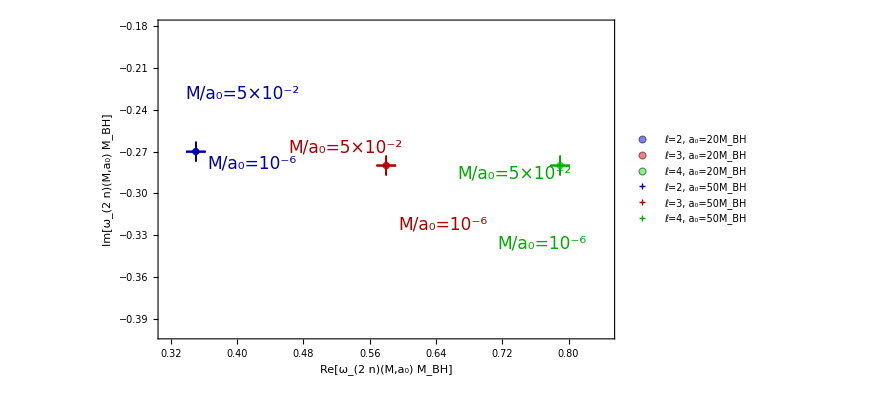

./plot/N=17 ReIm/3_all_l_over_n17_2.pdf

```mathematica
lTot=ListPlot[{ReIm20a0l2n1,ReIm20a0l3n1,ReIm20a0l4n1,ReIm104a0l2n1,ReIm104a0l3n1,ReIm104a0l4n1},Frame->True,ImageSize->650,PlotRange->{{0.315,0.845},{-0.40,-0.18}},FrameStyle->Directive[Thickness[0.0025],Black],FrameTicks->True,FrameLabel->{Style["Re[ω_ℓ1(M,a_0) M_BH]",Black,20],Style["Im[ω_ℓ1(M,a_0) M_BH]",Black,20]},FrameTicksStyle->Directive[Black,20],LabelStyle->{FontSize->19,FontFamily->"Times"},PlotMarkers->{Graphics[{Blue,Opacity[0.5],Thick,Disk[]},ImageSize->7],Graphics[{Red,Opacity[0.5],Thick,Disk[]},ImageSize->7],Graphics[{Green,Opacity[0.5],Thick,Disk[]},ImageSize->7],Style["+",{Darker@Blue,FontSize->20}],Style["+",{Darker@Red,FontSize->20}],Style["+",{Darker@Green,FontSize->20}]},PlotLegends->Placed[LineLegend[{Style["ℓ=2, a_0=20M_BH",FontSize->16],Style["ℓ=3, a_0=20M_BH",FontSize->16],Style["ℓ=4, a_0=20M_BH",FontSize->16],Style["ℓ=2, a_0=50M_BH",FontSize->16],Style["ℓ=3, a_0=50M_BH",FontSize->16],Style["ℓ=4, a_0=50M_BH",FontSize->16]},"Spacings"->{0.3}],{0.85,0.75}],Epilog->{Text[Style["M/a_0=5×10^-2",17,FontFamily->"Times",Darker@Blue],Scaled[{0.185,0.77}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Blue],Scaled[{0.205,0.55}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Red],Scaled[{0.625,0.36}]],Text[Style["M/a_0=5×10^-2",17,FontFamily->"Times",Darker@Red],Scaled[{0.41,0.60}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Green],Scaled[{0.84,0.30}]],Text[Style["M/a_0=5×10^-2",17,FontFamily->"Times",Darker@Green],Scaled[{0.78,0.52}]]}]
Export["./plot/N=17 ReIm/3_all_l_over_n17_2.pdf",%]
```

## Fixing Mhalo

## Finding modes

```mathematica
δωM[z_,l_,M_,ωtrial_]:=Block[{mbh=1,a0,ρmetric,f,m,fh,derfh,derrmh,rh,r,t0,ω,l0,s0,Mt0,Ml0,Ms0,FM0,eq,sol},

rh=2mbh(1+10^-4);
a0=M z^-1;

ρmetric=background["HQ",M,a0,10^10][[1,{1,3}]];

f[r_]=ρmetric[[1,2]][r];
m[r_]=ρmetric[[2,2]][r];

fh=0;
derfh=f'[rh];
derrmh=(D[ρprofile[r,M,a0,"HQ"],r]//.r->rh)*16 π;

t0=Table[f[-rh/(-1+x⟦i⟧)] (2 m[-rh/(-1+x⟦i⟧)]+rh/(-1+x⟦i⟧)) (1-x⟦i⟧)^3 (-1+x⟦i⟧)^2 x⟦i⟧,{i,2,n-1}]//FullSimplify;

l0=Table[1/(√(rh derfh))f[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧)^2 (2 m[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧) ((-1+x⟦i⟧) (-2+(1+4 ⅈ M ω) x⟦i⟧) √(rh derfh)+2 ⅈ rh ω (1-2 x⟦i⟧ (1+√(rh derfh))+x⟦i⟧^2 (1+√(rh derfh))))+rh (2 (-1+x⟦i⟧) (-1+(1+2 ⅈ M ω) x⟦i⟧) √(rh derfh)+2 ⅈ rh ω (1-2 x⟦i⟧ (1+√(rh derfh))+x⟦i⟧^2 (1+√(rh derfh)))-(-1+x⟦i⟧) x⟦i⟧ √(rh derfh)(m'[-rh/(-1+x⟦i⟧)]))),{i,2,n-1}]//FullSimplify;

s0=Table[1/(x⟦i⟧ derfh)f[-rh/(-1+x⟦i⟧)] (rh+2 m[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧)) ((-2+2 (5+2 ⅈ M ω+2 ⅈ rh ω) x⟦i⟧+(-20-17 ⅈ rh ω+4 M^2 ω^2+4 rh^2 ω^2+2 M ω (-9 ⅈ+4 rh ω)) x⟦i⟧^2-2 (-9-9 ⅈ rh ω+4 M^2 ω^2+2 rh^2 ω^2+6 M ω (-2 ⅈ+rh ω)) x⟦i⟧^3+(-6-5 ⅈ rh ω+4 M^2 ω^2+rh^2 ω^2+2 M ω (-5 ⅈ+2 rh ω)) x⟦i⟧^4) derfh+ω (-1+x⟦i⟧)^2 ((-1+x⟦i⟧) (3 ⅈ+(-5 ⅈ+4 M ω) x⟦i⟧) √(rh derfh)+rh ω (1-2 x⟦i⟧ (1+2 √(rh derfh))+x⟦i⟧^2 (1+2 √(rh derfh)))))+1/(√(rh derfh))f[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧) ((-1+x⟦i⟧) (-1+(2+2 ⅈ M ω) x⟦i⟧) √(rh derfh)+ⅈ rh ω (1-2 x⟦i⟧ (1+√(rh derfh))+x⟦i⟧^2 (1+√(rh derfh)))) (6 m[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧)+rh (2+m'[-rh/(-1+x⟦i⟧)]))+(1-x⟦i⟧)^3 x⟦i⟧ ((rh^3 ω^2)/(-1+x⟦i⟧)^3+f[-rh/(-1+x⟦i⟧)] (-6 m[-rh/(-1+x⟦i⟧)]-(rh (l+l^2+m'[-rh/(-1+x⟦i⟧)]))/(-1+x⟦i⟧))),{i,2,n-1}]//FullSimplify;

Mt0=t0*IdentityMatrix[n-2];
Ml0=l0*IdentityMatrix[n-2];
Ms0=s0*IdentityMatrix[n-2];

(*ωtrial=SetPrecision[0.37367-0.08897056I,50];*)
FM0=Mt0.df2+Ml0.df1+Ms0.df0;
eq=Det[N[FM0,80]];
sol=FindRoot[eq==0,{ω,ωtrial},WorkingPrecision->Precision[eq]];
PrintTemporary[{Re[sol[[1,2]]],Im[sol[[1,2]]]}];
Return[{z,Re[sol[[1,2]]],Im[sol[[1,2]]]}]
]
```

```mathematica
compactness=Range[-6,-1,1/2]
```

{-6,-11/2,-5,-9/2,-4,-7/2,-3,-5/2,-2,-3/2,-1}

```mathematica
datasetR[data_,thresh_]:=Select[Thread[{data[[2;;-1,1]],Abs[data[[2;;-1,2]]/data[[1,2]]-1]}],#[[1]]<=thresh&];
datasetI[data_,thresh_]:=Select[Thread[{data[[2;;-1,1]],Abs[data[[2;;-1,3]]/data[[1,3]]-1]}],#[[1]]<=thresh&];
```

#### fundamental

```mathematica
l2n0=Monitor[Table[δωM[10^compactness[[ii]],2,10^-1,SetPrecision[0.37-0.08I,50]],{ii,1,Length[compactness]}],ii];
```

Divide::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

FindRoot::jsing: Encountered a singular Jacobian at the point {ω} = {-0.91621688531074207479832310312058789897875130485-2.20650247504149108953804440400563570516475010278 ⅈ}. Try perturbing the initial point(s).

```mathematica
l3n0=Monitor[Table[δωM[10^compactness[[ii]],3,10^-1,SetPrecision[0.59-0.09I,50]],{ii,1,Length[compactness]}],ii];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50.7692 digits of working precision to meet these tolerances.

Divide::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

FindRoot::jsing: Encountered a singular Jacobian at the point {ω} = {0.97942404256880292008317069707539160777841319269307-1.6386118881047997863231432029806424023103816741292 ⅈ}. Try perturbing the initial point(s).

```mathematica
l4n0=Monitor[Table[δωM[10^compactness[[ii]],4,10^-1,SetPrecision[0.81-0.09I,50]],{ii,1,Length[compactness]}],ii];
```

Power::infy: Infinite expression 1/(0.+0. ⅈ)^5 encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {ω} = {-0.2812908626314010058107483878183072056164986990717-1.540259831203342581753839119313299619542907154139 ⅈ}.

Power::infy: Infinite expression 1/(0.+0. ⅈ)^5 encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {ω} = {-0.59682541193962754297634748842734024641988641536349-1.2367395454878288514669833366802732357339241024734 ⅈ}.

Divide::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {ω} = {-0.86888046970795832633594563874054210512942915956862-0.77958661043984911814067185529921119075554993746167 ⅈ}. Try perturbing the initial point(s).

```mathematica
ReImM01l2n0=l2n0[[;;,2;;3]];
ReImM01l3n0=l3n0[[;;,2;;3]];
ReImM01l4n0=l4n0[[;;,2;;3]];
```

#### first overtone

```mathematica
l2n1=Monitor[Table[δωM[10^compactness[[ii]],2,10^-1,SetPrecision[0.35-0.27I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
l3n1=Monitor[Table[δωM[10^compactness[[ii]],3,10^-1,SetPrecision[0.58-0.28I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
l4n1=Monitor[Table[δωM[10^compactness[[ii]],4,10^-1,SetPrecision[0.79-0.28I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
ReImM01l2n1=l2n1[[;;,2;;3]];
ReImM01l3n1=l3n1[[;;,2;;3]];
ReImM01l4n1=l4n1[[;;,2;;3]];
```

#### second overtone

```mathematica
l2n2=Monitor[Table[δωM[10^compactness[[ii]],2,10^-1,SetPrecision[0.3-0.47I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
l3n2=Monitor[Table[δωM[10^compactness[[ii]],3,10^-1,SetPrecision[0.56-0.48I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
l4n2=Monitor[Table[δωM[10^compactness[[ii]],4,10^-1,SetPrecision[0.80-0.48I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
ReImM01l2n2=l2n2[[;;,2;;3]];
ReImM01l3n2=l3n2[[;;,2;;3]];
ReImM01l4n2=l4n2[[;;,2;;3]];
```

## Finding modes (smaller M)

#### fundamental

```mathematica
l2n02=Monitor[Table[δωM[10^compactness[[ii]],2,10^-2,SetPrecision[0.37-0.08I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
l3n02=Monitor[Table[δωM[10^compactness[[ii]],3,10^-2,SetPrecision[0.59-0.09I,50]],{ii,1,Length[compactness]}],ii];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 49.7929 digits of working precision to meet these tolerances.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50.5198 digits of working precision to meet these tolerances.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50.6156 digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
l4n02=Monitor[Table[δωM[10^compactness[[ii]],4,10^-2,SetPrecision[0.81-0.09I,50]],{ii,1,Length[compactness]}],ii];
```

Divide::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

FindRoot::jsing: Encountered a singular Jacobian at the point {ω} = {0.81000000000000005329070518200751394033432006835938-1.9049846624323675456579278821591361648722533743915 ⅈ}. Try perturbing the initial point(s).

Divide::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

FindRoot::jsing: Encountered a singular Jacobian at the point {ω} = {0.81000000000000005329070518200751394033432006835938-1.9049846624323675456579278821591361648722533743915 ⅈ}. Try perturbing the initial point(s).

Divide::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Divide::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {ω} = {0.81000000000000005329070518200751394033432006835938-1.9049846624323675456579278821591361648722533743915 ⅈ}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

```mathematica
ReImM001l2n0=l2n02[[;;,2;;3]];
ReImM001l3n0=l3n02[[;;,2;;3]];
ReImM001l4n0=l4n02[[;;,2;;3]];
```

#### first overtone

```mathematica
l2n12=Monitor[Table[δωM[10^compactness[[ii]],2,10^-2,SetPrecision[0.35-0.27I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
l3n12=Monitor[Table[δωM[10^compactness[[ii]],3,10^-2,SetPrecision[0.58-0.28I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
l4n12=Monitor[Table[δωM[10^compactness[[ii]],4,10^-2,SetPrecision[0.79-0.28I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
ReImM001l2n1=l2n12[[;;,2;;3]];
ReImM001l3n1=l3n12[[;;,2;;3]];
ReImM001l4n1=l4n12[[;;,2;;3]];
```

#### second overtone

```mathematica
l2n22=Monitor[Table[δωM[10^compactness[[ii]],2,10^-2,SetPrecision[0.3-0.47I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
l3n22=Monitor[Table[δωM[10^compactness[[ii]],3,10^-2,SetPrecision[0.56-0.48I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
l4n22=Monitor[Table[δωM[10^compactness[[ii]],4,10^-2,SetPrecision[0.80-0.48I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
ReImM001l2n2=l2n22[[;;,2;;3]];
ReImM001l3n2=l3n22[[;;,2;;3]];
ReImM001l4n2=l4n22[[;;,2;;3]];
```

## Finding modes (higher M)

#### fundamental

```mathematica
l2n03=Monitor[Table[δωM[10^compactness[[ii]],2,10^-4,SetPrecision[0.37-0.08I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
l3n03=Monitor[Table[δωM[10^compactness[[ii]],3,10^-4,SetPrecision[0.59-0.09I,50]],{ii,1,Length[compactness]}],ii];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50.2093 digits of working precision to meet these tolerances.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 49.9823 digits of working precision to meet these tolerances.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 49.7005 digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
l4n03=Monitor[Table[δωM[10^compactness[[ii]],4,10^-4,SetPrecision[0.81-0.09I,50]],{ii,1,Length[compactness]}],ii];
```

Divide::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

FindRoot::jsing: Encountered a singular Jacobian at the point {ω} = {1.7968799141068189072991627201690384201618909978866-1.6132325364163060099125395941419373038275675662884 ⅈ}. Try perturbing the initial point(s).

Divide::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

FindRoot::jsing: Encountered a singular Jacobian at the point {ω} = {1.7962348927261831703648645909049874985068990574168-1.6136502424224889194660442491828171460596492813262 ⅈ}. Try perturbing the initial point(s).

Divide::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Divide::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {ω} = {1.794686107253413862921856539279042490258157697722-1.6146516307166216418379966561932572340435488062179 ⅈ}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

```mathematica
ReImM1l2n0=l2n03[[;;,2;;3]];
ReImM1l3n0=l3n03[[;;,2;;3]];
ReImM1l4n0=l4n03[[;;,2;;3]];
```

#### first overtone

```mathematica
l2n13=Monitor[Table[δωM[10^compactness[[ii]],2,10^-4,SetPrecision[0.35-0.27I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
l3n13=Monitor[Table[δωM[10^compactness[[ii]],3,10^-4,SetPrecision[0.58-0.28I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
l4n13=Monitor[Table[δωM[10^compactness[[ii]],4,10^-4,SetPrecision[0.79-0.28I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
ReImM1l2n1=l2n13[[;;,2;;3]];
ReImM1l3n1=l3n13[[;;,2;;3]];
ReImM1l4n1=l4n13[[;;,2;;3]];
```

## plots (fixed M)

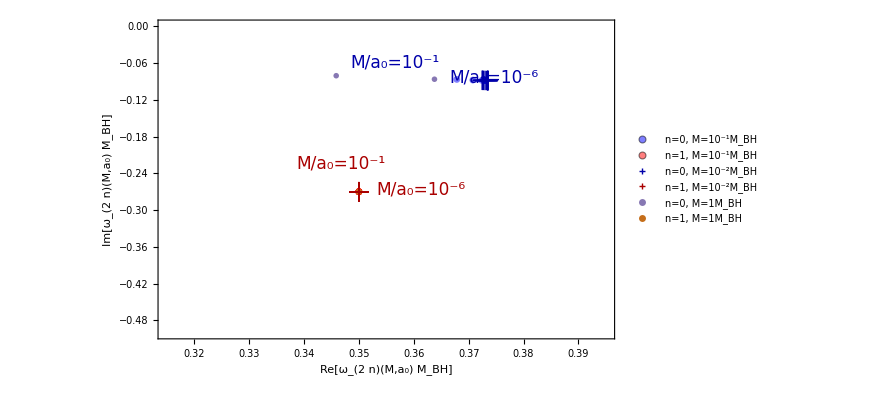

./plot/N=17 ReIm/M_l2_cp_n17.pdf

```mathematica
l2=ListPlot[{ReImM01l2n0,ReImM01l2n1,ReImM001l2n0,ReImM001l2n1,ReImM1l2n0,ReImM1l2n1},Frame->True,ImageSize->650,PlotRange->{{0.315,0.395},{-0.5,0.0}},FrameStyle->Directive[Thickness[0.0025],Black],FrameTicks->True,FrameLabel->{Style["Re[ω_(2  n)(M,a_0) M_BH]",Black,20],Style["Im[ω_(2  n)(M,a_0) M_BH]",Black,20]},FrameTicksStyle->Directive[Black,20],LabelStyle->{FontSize->19,FontFamily->"Times"},PlotMarkers->{Graphics[{Blue,Opacity[0.5],Thick,Disk[]},ImageSize->7],Graphics[{Red,Opacity[0.5],Thick,Disk[]},ImageSize->7],Style["+",{Darker@Blue,FontSize->20}],Style["+",{Darker@Red,FontSize->20}],Style["x",{Blue,FontSize->20}],Style["x",{Red,FontSize->20}]},PlotLegends->Placed[LineLegend[{Style["n=0, M=10^-1M_BH",FontSize->16],Style["n=1, M=10^-1M_BH",FontSize->16],Style["n=0, M=10^-2M_BH",FontSize->16],Style["n=1, M=10^-2M_BH",FontSize->16],Style["n=0, M=1M_BH",FontSize->16],Style["n=1, M=1M_BH",FontSize->16]},"Spacings"->{0.3}],{0.15,0.75}],Epilog->{Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Blue],Scaled[{0.52,0.867}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Blue],Scaled[{0.735,0.82}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Red],Scaled[{0.575,0.47}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Red],Scaled[{0.4,0.55}]](*,Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Green],Scaled[{0.45,0.07}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Green],Scaled[{0.1,0.16}]]*)}]
Export["./plot/N=17 ReIm/M_l2_cp_n17.pdf",%]
```

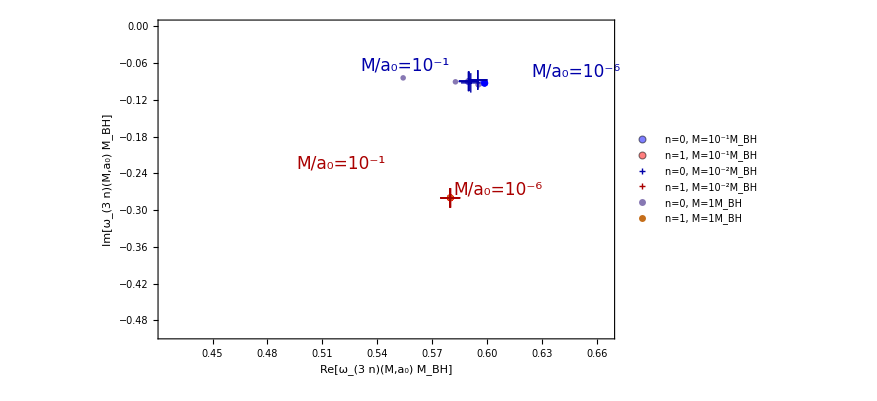

./plot/N=17 ReIm/M_l3_cp_n17.pdf

```mathematica
l3=ListPlot[{ReImM01l3n0,ReImM01l3n1,ReImM001l3n0,ReImM001l3n1,ReImM1l3n0,ReImM1l3n1},Frame->True,ImageSize->650,PlotRange->{{0.425,0.665},{-0.5,0.0}},FrameStyle->Directive[Thickness[0.0025],Black],FrameTicks->True,FrameLabel->{Style["Re[ω_(3  n)(M,a_0) M_BH]",Black,20],Style["Im[ω_(3  n)(M,a_0) M_BH]",Black,20]},FrameTicksStyle->Directive[Black,20],LabelStyle->{FontSize->19,FontFamily->"Times"},PlotMarkers->{Graphics[{Blue,Opacity[0.5],Thick,Disk[]},ImageSize->7],Graphics[{Red,Opacity[0.5],Thick,Disk[]},ImageSize->7],Style["+",{Darker@Blue,FontSize->20}],Style["+",{Darker@Red,FontSize->20}],Style["x",{Blue,FontSize->20}],Style["x",{Red,FontSize->20}],Style["+",{Darker@Green,FontSize->20}]},PlotLegends->Placed[LineLegend[{Style["n=0, M=10^-1M_BH",FontSize->16],Style["n=1, M=10^-1M_BH",FontSize->16],Style["n=0, M=10^-2M_BH",FontSize->16],Style["n=1, M=10^-2M_BH",FontSize->16],Style["n=0, M=1M_BH",FontSize->16],Style["n=1, M=1M_BH",FontSize->16]},"Spacings"->{0.3}],{0.15,0.75}],Epilog->{Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Blue],Scaled[{0.54,0.857}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Blue],Scaled[{0.915,0.84}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Red],Scaled[{0.745,0.47}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Red],Scaled[{0.4,0.55}]](*,Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Green],Scaled[{0.45,0.07}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Green],Scaled[{0.1,0.16}]]*)}]
Export["./plot/N=17 ReIm/M_l3_cp_n17.pdf",%]
```

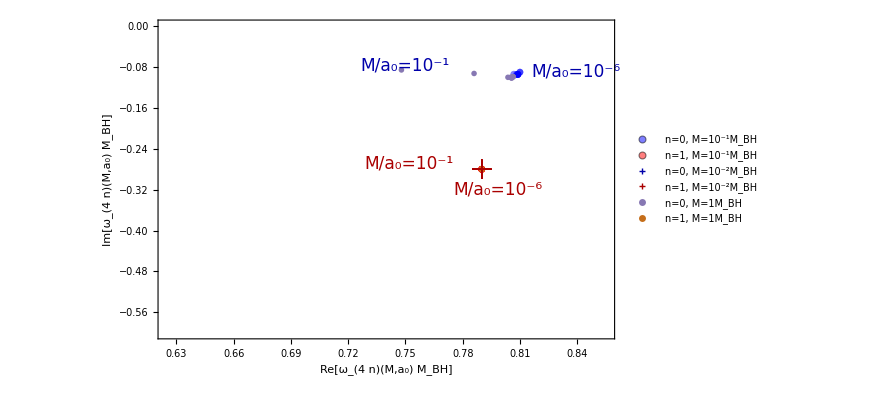

./plot/N=17 ReIm/M_l4_cp_n17.pdf

```mathematica
l4=ListPlot[{ReImM01l4n0,ReImM01l4n1,ReImM001l4n0,ReImM001l4n1,ReImM1l4n0,ReImM1l4n1},Frame->True,ImageSize->650,PlotRange->{{0.625,0.855},{-0.6,0.0}},FrameStyle->Directive[Thickness[0.0025],Black],FrameTicks->True,FrameLabel->{Style["Re[ω_(4  n)(M,a_0) M_BH]",Black,20],Style["Im[ω_(4  n)(M,a_0) M_BH]",Black,20]},FrameTicksStyle->Directive[Black,20],LabelStyle->{FontSize->19,FontFamily->"Times"},PlotMarkers->{Graphics[{Blue,Opacity[0.5],Thick,Disk[]},ImageSize->7],Graphics[{Red,Opacity[0.5],Thick,Disk[]},ImageSize->7],Style["+",{Darker@Blue,FontSize->20}],Style["+",{Darker@Red,FontSize->20}],Style["x",{Blue,FontSize->20}],Style["x",{Red,FontSize->20}],Style["+",{Darker@Green,FontSize->20}]},PlotLegends->Placed[LineLegend[{Style["n=0, M=10^-1M_BH",FontSize->16],Style["n=1, M=10^-1M_BH",FontSize->16],Style["n=0, M=10^-2M_BH",FontSize->16],Style["n=1, M=10^-2M_BH",FontSize->16],Style["n=0, M=1M_BH",FontSize->16],Style["n=1, M=1M_BH",FontSize->16]},"Spacings"->{0.3}],{0.15,0.75}],Epilog->{Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Blue],Scaled[{0.54,0.857}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Blue],Scaled[{0.915,0.84}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Red],Scaled[{0.745,0.47}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Red],Scaled[{0.55,0.55}]](*,Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Green],Scaled[{0.45,0.07}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Green],Scaled[{0.1,0.16}]]*)}]
Export["./plot/N=17 ReIm/M_l4_cp_n17.pdf",%]
```

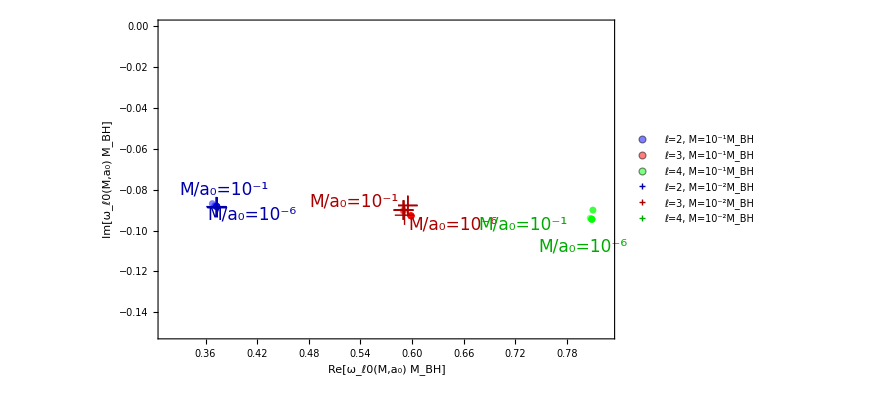

./plot/N=17 ReIm/M_all_l_cp_n17.pdf

```mathematica
lTot=ListPlot[{ReImM01l2n0,ReImM01l3n0,ReImM01l4n0,ReImM001l2n0,ReImM001l3n0,ReImM001l4n0},Frame->True,ImageSize->650,PlotRange->{{0.315,0.825},{-0.15,0.0}},FrameStyle->Directive[Thickness[0.0025],Black],FrameTicks->True,FrameLabel->{Style["Re[ω_ℓ0(M,a_0) M_BH]",Black,20],Style["Im[ω_ℓ0(M,a_0) M_BH]",Black,20]},FrameTicksStyle->Directive[Black,20],LabelStyle->{FontSize->19,FontFamily->"Times"},PlotMarkers->{Graphics[{Blue,Opacity[0.5],Thick,Disk[]},ImageSize->7],Graphics[{Red,Opacity[0.5],Thick,Disk[]},ImageSize->7],Graphics[{Green,Opacity[0.5],Thick,Disk[]},ImageSize->7],Style["+",{Darker@Blue,FontSize->20}],Style["+",{Darker@Red,FontSize->20}],Style["+",{Darker@Green,FontSize->20}]},PlotLegends->Placed[LineLegend[{Style["ℓ=2, M=10^-1M_BH",FontSize->16],Style["ℓ=3, M=10^-1M_BH",FontSize->16],Style["ℓ=4, M=10^-1M_BH",FontSize->16],Style["ℓ=2, M=10^-2M_BH",FontSize->16],Style["ℓ=3, M=10^-2M_BH",FontSize->16],Style["ℓ=4, M=10^-2M_BH",FontSize->16]},"Spacings"->{0.3}],{0.85,0.75}],Epilog->{Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Blue],Scaled[{0.145,0.47}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Blue],Scaled[{0.205,0.39}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Red],Scaled[{0.645,0.36}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Red],Scaled[{0.43,0.43}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Green],Scaled[{0.93,0.29}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Green],Scaled[{0.8,0.36}]]}]
Export["./plot/N=17 ReIm/M_all_l_cp_n17.pdf",%]
```

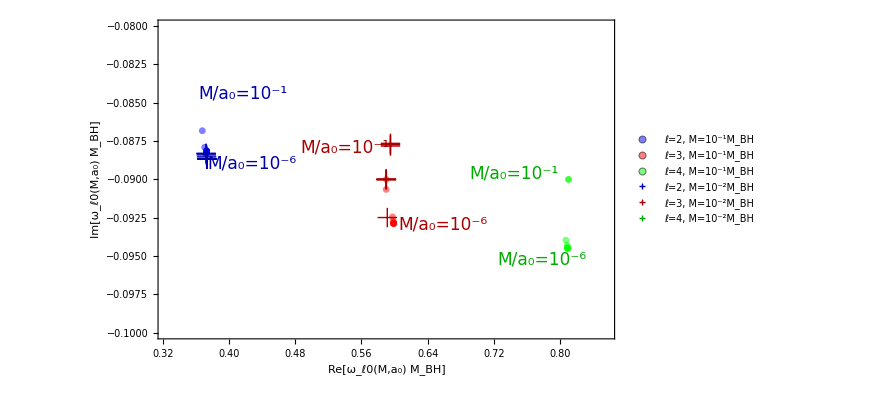

./plot/N=17 ReIm/M_all_l_cp_n17_2.pdf

```mathematica
lTot=ListPlot[{ReImM01l2n0,ReImM01l3n0,ReImM01l4n0,ReImM001l2n0,ReImM001l3n0,ReImM001l4n0},Frame->True,ImageSize->650,PlotRange->{{0.325,0.855},{-0.1,-0.08}},FrameStyle->Directive[Thickness[0.0025],Black],FrameTicks->True,FrameLabel->{Style["Re[ω_ℓ0(M,a_0) M_BH]",Black,20],Style["Im[ω_ℓ0(M,a_0) M_BH]",Black,20]},FrameTicksStyle->Directive[Black,20],LabelStyle->{FontSize->19,FontFamily->"Times"},PlotMarkers->{Graphics[{Blue,Opacity[0.5],Thick,Disk[]},ImageSize->7],Graphics[{Red,Opacity[0.5],Thick,Disk[]},ImageSize->7],Graphics[{Green,Opacity[0.5],Thick,Disk[]},ImageSize->7],Style["+",{Darker@Blue,FontSize->20}],Style["+",{Darker@Red,FontSize->20}],Style["+",{Darker@Green,FontSize->20}]},PlotLegends->Placed[LineLegend[{Style["ℓ=2, M=10^-1M_BH",FontSize->16],Style["ℓ=3, M=10^-1M_BH",FontSize->16],Style["ℓ=4, M=10^-1M_BH",FontSize->16],Style["ℓ=2, M=10^-2M_BH",FontSize->16],Style["ℓ=3, M=10^-2M_BH",FontSize->16],Style["ℓ=4, M=10^-2M_BH",FontSize->16]},"Spacings"->{0.3}],{0.85,0.78}],Epilog->{Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Blue],Scaled[{0.185,0.77}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Blue],Scaled[{0.205,0.55}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Red],Scaled[{0.625,0.36}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Red],Scaled[{0.41,0.60}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Green],Scaled[{0.84,0.25}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Green],Scaled[{0.78,0.52}]]}]
Export["./plot/N=17 ReIm/M_all_l_cp_n17_2.pdf",%]
```

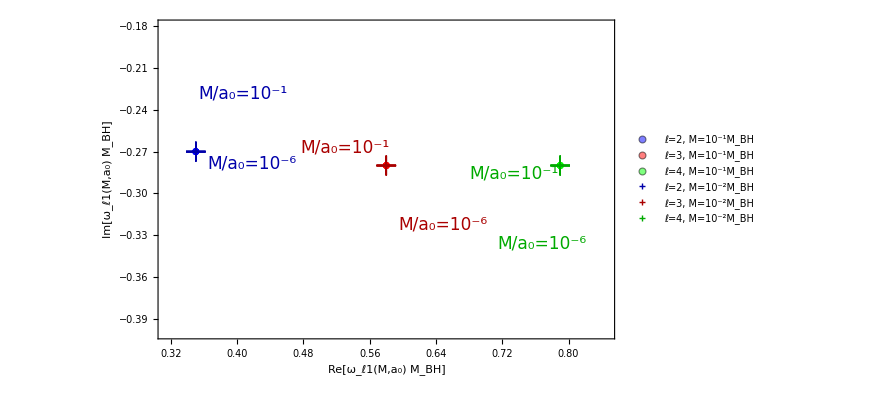

./plot/N=17 ReIm/M_all_l_over_n17.pdf

```mathematica
lTot=ListPlot[{ReImM01l2n1,ReImM01l3n1,ReImM01l4n1,ReImM001l2n1,ReImM001l3n1,ReImM001l4n1},Frame->True,ImageSize->650,PlotRange->{{0.315,0.845},{-0.40,-0.18}},FrameStyle->Directive[Thickness[0.0025],Black],FrameTicks->True,FrameLabel->{Style["Re[ω_ℓ1(M,a_0) M_BH]",Black,20],Style["Im[ω_ℓ1(M,a_0) M_BH]",Black,20]},FrameTicksStyle->Directive[Black,20],LabelStyle->{FontSize->19,FontFamily->"Times"},PlotMarkers->{Graphics[{Blue,Opacity[0.5],Thick,Disk[]},ImageSize->7],Graphics[{Red,Opacity[0.5],Thick,Disk[]},ImageSize->7],Graphics[{Green,Opacity[0.5],Thick,Disk[]},ImageSize->7],Style["+",{Darker@Blue,FontSize->20}],Style["+",{Darker@Red,FontSize->20}],Style["+",{Darker@Green,FontSize->20}]},PlotLegends->Placed[LineLegend[{Style["ℓ=2, M=10^-1M_BH",FontSize->16],Style["ℓ=3, M=10^-1M_BH",FontSize->16],Style["ℓ=4, M=10^-1M_BH",FontSize->16],Style["ℓ=2, M=10^-2M_BH",FontSize->16],Style["ℓ=3, M=10^-2M_BH",FontSize->16],Style["ℓ=4, M=10^-2M_BH",FontSize->16]},"Spacings"->{0.3}],{0.85,0.75}],Epilog->{Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Blue],Scaled[{0.185,0.77}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Blue],Scaled[{0.205,0.55}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Red],Scaled[{0.625,0.36}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Red],Scaled[{0.41,0.60}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Green],Scaled[{0.84,0.30}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Green],Scaled[{0.78,0.52}]]}]
Export["./plot/N=17 ReIm/M_all_l_over_n17.pdf",%]
```

```mathematica
l2n02Vac=δωM[10^-8,2,10^-2,SetPrecision[0.37-0.08I,50]];
l2n0Vac=δωM[10^-8,2,10^-1,SetPrecision[0.37-0.08I,50]];
l2n03Vac=δωM[10^-7,2,10^-4,SetPrecision[0.37-0.08I,50]];
ReImM01l2n0Vac=l2n0Vac[[2;;3]]
ReImM001l2n0Vac=l2n02Vac[[2;;3]]
ReImM1l2n0Vac=l2n03Vac[[2;;3]]
M01corrl2=Monitor[Table[ReImM001l2n0Vac-(ReImM01l2n0Vac-ReImM01l2n0[[ii]]),{ii,1,Length[compactness]-1}],ii];
M001corrl2=Monitor[Table[ReImM001l2n0Vac-(ReImM001l2n0Vac-ReImM001l2n0[[ii]]),{ii,1,Length[compactness]}],ii];
M1corrl2=Monitor[Table[ReImM001l2n0Vac-(ReImM1l2n0Vac-ReImM1l2n0[[ii]]),{ii,1,Length[compactness]}],ii];
```

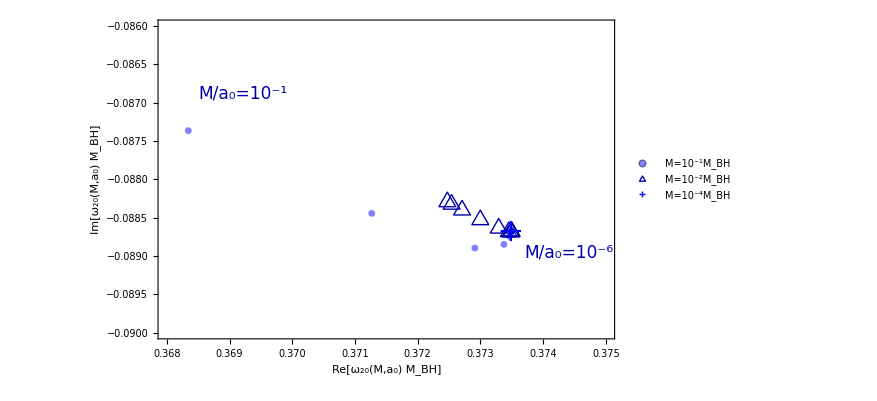

./plot/N=17 ReIm/M_l2_cp_n17.pdf

```mathematica
lTot=ListPlot[{M01corrl2,M001corrl2,M1corrl2},Frame->True,ImageSize->650,PlotRange->{{0.368,0.375},{-0.09,-0.086}},FrameStyle->Directive[Thickness[0.0025],Black],FrameTicks->True,FrameLabel->{Style["Re[ω_20(M,a_0) M_BH]",Black,20],Style["Im[ω_20(M,a_0) M_BH]",Black,20]},FrameTicksStyle->Directive[Black,20],LabelStyle->{FontSize->19,FontFamily->"Times"},PlotMarkers->{Graphics[{Blue,Opacity[0.5],Thick,Disk[]},ImageSize->7],(*Graphics[{Red,Opacity[0.5],Thick,Disk[]},ImageSize->7],Graphics[{Green,Opacity[0.5],Thick,Disk[]},ImageSize->7],*)Style["△",{Darker@Blue,FontSize->20}],Style["+",{Blue,FontSize->20}],Style["+",{Darker@Green,FontSize->20}]},PlotLegends->Placed[LineLegend[{Style["M=10^-1M_BH",FontSize->16],Style["M=10^-2M_BH",FontSize->16],Style["M=10^-4M_BH",FontSize->16],Style["ℓ=2, M=10^-2M_BH",FontSize->16],Style["ℓ=3, M=10^-2M_BH",FontSize->16],Style["ℓ=4, M=10^-2M_BH",FontSize->16]},"Spacings"->{0.3}],{0.85,0.78}],Epilog->{Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Blue],Scaled[{0.185,0.77}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Blue],Scaled[{0.9,0.27}]](*,Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Red],Scaled[{0.625,0.36}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Red],Scaled[{0.41,0.60}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Green],Scaled[{0.84,0.25}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Green],Scaled[{0.78,0.52}]]*)}]
Export["./plot/N=17 ReIm/M_l2_cp_n17.pdf",%]
```

```mathematica
l3n02Vac=δωM[10^-8,3,10^-2,SetPrecision[0.37-0.08I,50]];
l3n0Vac=δωM[10^-8,3,10^-1,SetPrecision[0.37-0.08I,50]];
l3n03Vac=δωM[10^-8,3,10^-4,SetPrecision[0.37-0.08I,50]];
ReImM01l3n0Vac=l3n0Vac[[2;;3]]
ReImM001l3n0Vac=l3n02Vac[[2;;3]]
ReImM1l3n0Vac=l3n03Vac[[2;;3]]
M01corrl3=Monitor[Table[ReImM001l3n0Vac-(ReImM01l3n0Vac-ReImM01l3n0[[ii]]),{ii,1,Length[compactness]-1}],ii];
M001corrl3=Monitor[Table[ReImM001l3n0Vac-(ReImM001l3n0Vac-ReImM001l3n0[[ii]]),{ii,1,Length[compactness]}],ii];
M1corrl3=Monitor[Table[ReImM1l3n0Vac-(ReImM1l3n0Vac-ReImM1l3n0[[ii]]),{ii,1,Length[compactness]}],ii];
```

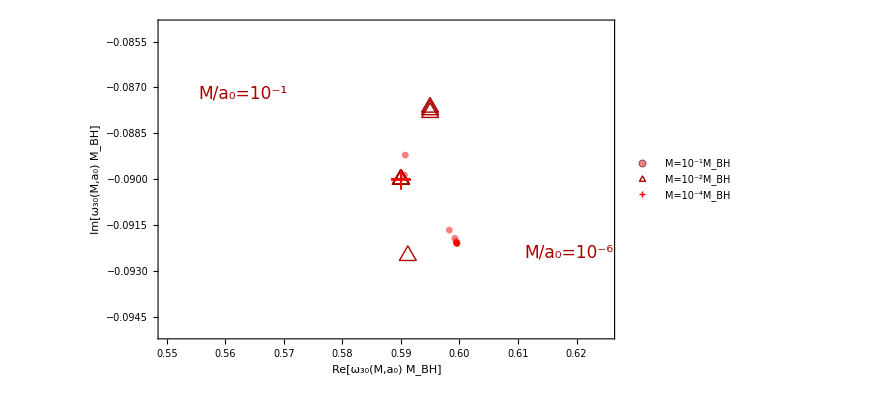

./plot/N=17 ReIm/M_l3_cp_n17.pdf

```mathematica
lTot3=ListPlot[{M01corrl3,M001corrl3,M1corrl3},Frame->True,ImageSize->650,PlotRange->{{0.55,0.625},{-0.095,-0.085}},FrameStyle->Directive[Thickness[0.0025],Black],FrameTicks->True,FrameLabel->{Style["Re[ω_30(M,a_0) M_BH]",Black,20],Style["Im[ω_30(M,a_0) M_BH]",Black,20]},FrameTicksStyle->Directive[Black,20],LabelStyle->{FontSize->19,FontFamily->"Times"},PlotMarkers->{Graphics[{Red,Opacity[0.5],Thick,Disk[]},ImageSize->7],(*Graphics[{Red,Opacity[0.5],Thick,Disk[]},ImageSize->7],Graphics[{Green,Opacity[0.5],Thick,Disk[]},ImageSize->7],*)Style["△",{Darker@Red,FontSize->20}],Style["+",{Red,FontSize->20}],Style["+",{Darker@Green,FontSize->20}]},PlotLegends->Placed[LineLegend[{Style["M=10^-1M_BH",FontSize->16],Style["M=10^-2M_BH",FontSize->16],Style["M=10^-4M_BH",FontSize->16],Style["ℓ=2, M=10^-2M_BH",FontSize->16],Style["ℓ=3, M=10^-2M_BH",FontSize->16],Style["ℓ=4, M=10^-2M_BH",FontSize->16]},"Spacings"->{0.3}],{0.85,0.78}],Epilog->{Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Red],Scaled[{0.185,0.77}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Red],Scaled[{0.9,0.27}]](*,Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Red],Scaled[{0.625,0.36}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Red],Scaled[{0.41,0.60}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Green],Scaled[{0.84,0.25}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Green],Scaled[{0.78,0.52}]]*)}]
Export["./plot/N=17 ReIm/M_l3_cp_n17.pdf",%]
```

```mathematica
l4n02Vac=δωM[10^-8,4,10^-2,SetPrecision[0.37-0.08I,50]];
l4n0Vac=δωM[10^-8,4,10^-1,SetPrecision[0.37-0.08I,50]];
l4n03Vac=δωM[10^-8,4,10^-4,SetPrecision[0.37-0.08I,50]];
ReImM01l4n0Vac=l4n0Vac[[2;;3]]
ReImM001l4n0Vac=l4n02Vac[[2;;3]]
ReImM1l4n0Vac=l4n03Vac[[2;;3]]
M01corrl4=Monitor[Table[ReImM001l4n0Vac-(ReImM01l4n0Vac-ReImM01l4n0[[ii]]),{ii,1,Length[compactness]-1}],ii];
M001corrl4=Monitor[Table[ReImM01l4n0Vac-(ReImM001l4n0Vac-ReImM001l4n0[[ii]]),{ii,1,Length[compactness]}],ii];
M1corrl4=Monitor[Table[ReImM1l4n0Vac-(ReImM1l4n0Vac-ReImM1l4n0[[ii]]),{ii,1,Length[compactness]}],ii];
```

Divide::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

FindRoot::jsing: Encountered a singular Jacobian at the point {ω} = {0.35458873901789742635774582928570414053166271245142-0.19949689605071195448417302197114194050334816676488 ⅈ}. Try perturbing the initial point(s).

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 51.1747 digits of working precision to meet these tolerances.

Divide::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

FindRoot::jsing: Encountered a singular Jacobian at the point {ω} = {0.35471296915002755730228798053150116653424574929277-0.19938014317965851032217279424915009664901820766013 ⅈ}. Try perturbing the initial point(s).

{0.353437472989922743326780849297159905774470557156949,-0.200553345442676674422640109933838837436950528326387}

{0.35458873901789742635774582928570414053166271245142,-0.19949689605071195448417302197114194050334816676488}

{0.35471296915002755730228798053150116653424574929277,-0.19938014317965851032217279424915009664901820766013}

```mathematica
M001corrl4=Monitor[Table[ReImM01l4n0Vac-(ReImM001l4n0Vac-ReImM001l4n0[[ii]]),{ii,1,Length[compactness]}],ii];
```

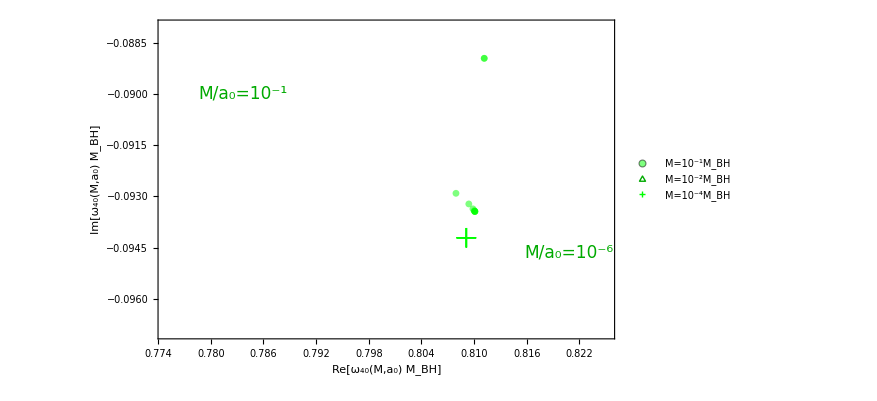

./plot/N=17 ReIm/M_l4_cp_n17.pdf

```mathematica
lTot4=ListPlot[{M01corrl4,M001corrl4,M1corrl4},Frame->True,ImageSize->650,PlotRange->{{0.775,0.825},{-0.097,-0.088}},FrameStyle->Directive[Thickness[0.0025],Black],FrameTicks->True,FrameLabel->{Style["Re[ω_40(M,a_0) M_BH]",Black,20],Style["Im[ω_40(M,a_0) M_BH]",Black,20]},FrameTicksStyle->Directive[Black,20],LabelStyle->{FontSize->19,FontFamily->"Times"},PlotMarkers->{Graphics[{Green,Opacity[0.5],Thick,Disk[]},ImageSize->7],(*Graphics[{Green,Opacity[0.5],Thick,Disk[]},ImageSize->7],Graphics[{Green,Opacity[0.5],Thick,Disk[]},ImageSize->7],*)Style["△",{Darker@Green,FontSize->20}],Style["+",{Green,FontSize->20}],Style["+",{Darker@Green,FontSize->20}]},PlotLegends->Placed[LineLegend[{Style["M=10^-1M_BH",FontSize->16],Style["M=10^-2M_BH",FontSize->16],Style["M=10^-4M_BH",FontSize->16],Style["ℓ=2, M=10^-2M_BH",FontSize->16],Style["ℓ=3, M=10^-2M_BH",FontSize->16],Style["ℓ=4, M=10^-2M_BH",FontSize->16]},"Spacings"->{0.3}],{0.85,0.78}],Epilog->{Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Green],Scaled[{0.185,0.77}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Green],Scaled[{0.9,0.27}]](*,Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Red],Scaled[{0.625,0.36}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Red],Scaled[{0.41,0.60}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Green],Scaled[{0.84,0.25}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Green],Scaled[{0.78,0.52}]]*)}]
Export["./plot/N=17 ReIm/M_l4_cp_n17.pdf",%]
```

```mathematica
ReImM001l4n0
```

{{0.81000000000000005329070518200751394033432006835938,-1.9049846624323675456579278821591361648722533743915},{0.81000000000000005329070518200751394033432006835938,-1.9049846624323675456579278821591361648722533743915},{0.81000000000000005329070518200751394033432006835938,-1.9049846624323675456579278821591361648722533743915},{0.81000000000000005329070518200751394033432006835938,-1.9049846624323675456579278821591361648722533743915},{0.810000000000000053290705182007513940334320068359375,-1.90498466243236754565792788215913616487225337439149},{0.81000000000000005329070518200751394033432006835938,-1.9049846624323675456579278821591361648722533743915},{1.5593354527714030853645070129718789171544286756955,-1.7430776461148494971125741437663360156113692057132},{0.81000000000000005329070518200751394033432006835938,-1.9049846624323675456579278821591361648722533743915},{0.81000000000000005329070518200751394033432006835938,-1.9049846624323675456579278821591361648722533743915},{0.81000000000000005329070518200751394033432006835938,-1.9049846624323675456579278821591361648722533743915},{0.81000000000000005329070518200751394033432006835938,-1.9049846624323675456579278821591361648722533743915}}

```mathematica
M001corrl4
```

{{0.8088487339720253702597402020189697055771279130649,-1.906041111824332265596394970121833061805855735953},{0.8088487339720253702597402020189697055771279130649,-1.906041111824332265596394970121833061805855735953},{0.8088487339720253702597402020189697055771279130649,-1.906041111824332265596394970121833061805855735953},{0.8088487339720253702597402020189697055771279130649,-1.906041111824332265596394970121833061805855735953},{0.8088487339720253702597402020189697055771279130649,-1.906041111824332265596394970121833061805855735953},{0.8088487339720253702597402020189697055771279130649,-1.906041111824332265596394970121833061805855735953},{1.558184186743428402333542032983334682397236520401,-1.7441340955068142170510412317290329125449715672747},{0.8088487339720253702597402020189697055771279130649,-1.906041111824332265596394970121833061805855735953},{0.8088487339720253702597402020189697055771279130649,-1.906041111824332265596394970121833061805855735953},{0.8088487339720253702597402020189697055771279130649,-1.906041111824332265596394970121833061805855735953},{0.8088487339720253702597402020189697055771279130649,-1.906041111824332265596394970121833061805855735953}}